```mathematica
(* Set the folder for saving gifs *)
SetDirectory@NotebookDirectory[];
```

```mathematica
(* Function finding EV stops corresponding to min and max values and plotting them *)
plotDynamicRange[f_,minValFinal_,maxValFinal_,plotMinRange_,plotMaxRange_]:=Module[{minValue,maxValue},{Set @@@Solve[Rationalize[f[Power[2,minValue]]==minValFinal&&f[Power[2,maxValue]]==maxValFinal],{minValue,maxValue},Reals][[1]];
{ListPlot[Table[{x,f[Power[2,x]]},{x,Ceiling[minValue],Floor[maxValue]}],PlotStyle->PointSize[0.02],PlotRange->{{plotMinRange,plotMaxRange},{-0.1,1.1}},ImageSize->600],
Graphics[Text[StringForm["Function            = `1`",f],{plotMinRange,0.6},{-1,0}]],Graphics[Text[StringForm["Min value         = `1`",N[minValue]],{plotMinRange,0.5},{-1,0}]],
Graphics[Text[StringForm["Max value         = `1`",N[maxValue]],{plotMinRange,0.4},{-1,0}]],
Graphics[Text[StringForm["Dynamic range = `1`",N[maxValue-minValue]],{plotMinRange,0.3},{-1,0}]],
Graphics[{Red,Arrowheads[{-0.03,.03}],Thickness->0.005,Arrow[{{minValue,-0.05},{maxValue,-0.05}}]}],
Table[Graphics[{Green,Thickness->0.005,Line[{{y,-0.01},{y,0.03}}]}],{y,Ceiling[minValue],Floor[maxValue]}],
Table[Graphics[{Blue,Thickness->0.005,Line[{{-(plotMaxRange-plotMinRange)/100.0,f[Power[2,z]]},{(plotMaxRange-plotMinRange)/100.0,f[Power[2,z]]}}]}],{z,Ceiling[minValue],Floor[maxValue]}]
}}]
```

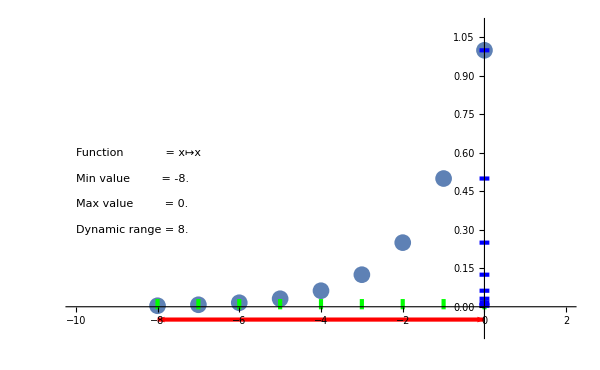

```mathematica
(* Display dynamic range for linear encoding, no gamma *)
Show[plotDynamicRange[Function[x,x],1/256,1,-10,2]]
```

```mathematica
(* Display how exposure just shifts the dynamic range *)
Animate[y=N[2^-a];Show[Quiet@plotDynamicRange[Function[x,Evaluate[y*x]],1/256,1,-10,2]],{a,-2,2,0.05}]
```

```mathematica
(* Save it to a gif file *)
Quiet@Export["exposure.gif",Table[y=N[2^-a];Show[plotDynamicRange[Function[x,Evaluate[y*x]],1/256,1,-10,2]],{a,-2,2,0.05}]];
```

```mathematica
(* Display how gamma affects dynamic range - stretching and squishing it *)
Animate[Show[plotDynamicRange[Function[x,Evaluate[Power[x,a]]],1/256,1,-10,2]],{a,0.8,2.0,0.02}]
```

```mathematica
(* Save it to a gif file *)
Quiet@Export["gamma.gif",Table[Show[plotDynamicRange[Function[x,Power[x,a]],1/256,1,-10,2]],{a,0.8,2.0,0.02}]];
```

```mathematica
(* Define a "gammaShift" function, gamma + exposure shift, so a contrast operation *)
gammaShift[x_,g_,p_]:=Power[x,g]/Power[p,g]*p
```

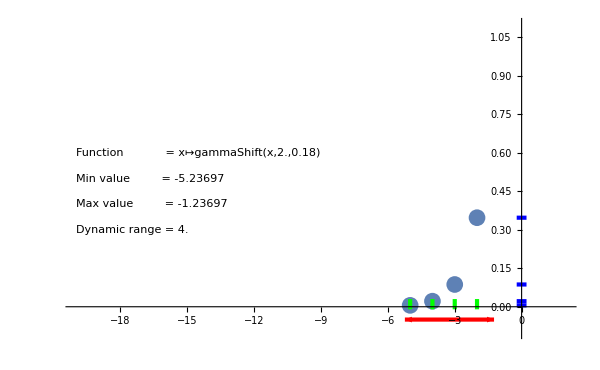

```mathematica
(* Show an example of increasing the contrast*)
Show[Quiet@plotDynamicRange[Function[x,gammaShift[x,2.0,0.18]],1/256,1,-20,2]]
```

```mathematica
(* Animation example of contrast *)

Animate[Show[Quiet@plotDynamicRange[Function[x,Evaluate[gammaShift[x,a,0.18]]],1/256,1,-10,2]],{a,1.0,2.0,0.02}]
```

```mathematica
(* Save it to a gif *)
Export["contrast.gif",Table[Quiet@Show[plotDynamicRange[Function[x,Evaluate[gammaShift[x,a,0.18]]],1/256,1,-10,2]],{a,1.0,2.0,0.02}]];
```

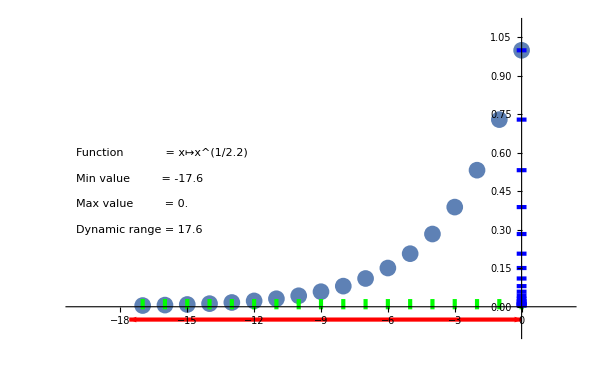

```mathematica
(* Display how gamma 2.2 affects the dynamic range *)
Show[plotDynamicRange[Function[x,Power[x,1/2.2]],1/256,1,-20,2]]
```

```mathematica
(* Display the difference between gamma 2.2 and 2.4 *)
ListAnimate[Map[Function[y,Show[plotDynamicRange[Function[x,Power[x,y]],1/256,1,-20,2]]],{1/2.2,1/2.4}]]
```

```mathematica
(* Save it to a gif file *)
Export["gamma_2_2vs2_4.gif",Map[Function[y,Show[plotDynamicRange[Function[x,Power[x,y]],1/256,1,-20,2]]],{1/2.2,1/2.4}],"DisplayDurations"->2];
```

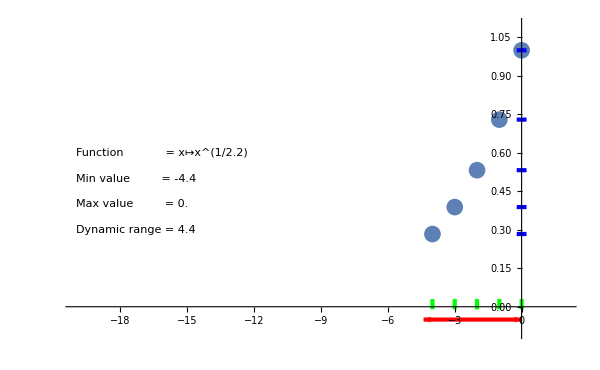

```mathematica
(* Simulate poor viewing conditions by cutting off bottom 25% of encoding range *)
Show[plotDynamicRange[Function[x,Power[x,1/2.2]],64/256,1,-20,2]]
```

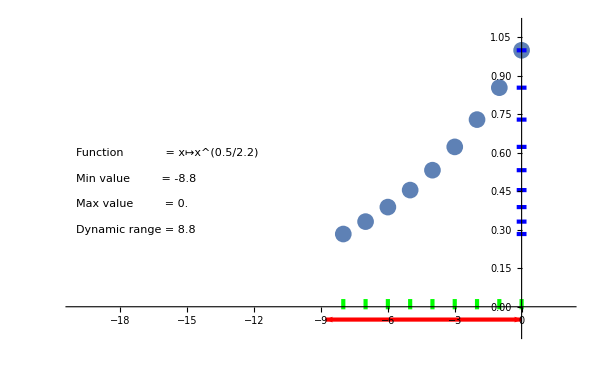

```mathematica
(* Now the same with some extra user specified gamma settings *)
Show[plotDynamicRange[Function[x,Power[x,0.5/2.2]],64/256,1,-20,2]]
```

```mathematica
(* Compare them 1 to 1 *)
ListAnimate[Map[Function[y,Show[plotDynamicRange[Function[x,Power[x,y]],64/256,1,-20,2]]],{1/2.2,0.7/2.2}]]
```

```mathematica
(* And save to a gif file *)
Export["poor_viewing_conditions.gif",Map[Function[y,Show[plotDynamicRange[Function[x,Power[x,y]],64/256,1,-20,2]]],{1/2.2,0.7/2.2}],"DisplayDurations"->2];
```

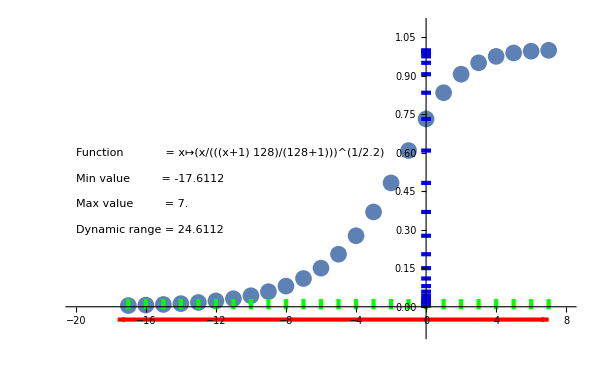

```mathematica
(* Demonstrate effect of Reinhard simple x/(1+x) operator with whitepoint of 128 *)

Show[Quiet@plotDynamicRange[Function[x,Power[x/(1+x) * (1/(128/(128+1))),1/2.2]],1/256,1,-20,8]]
```